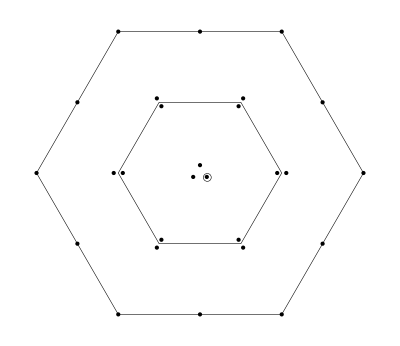

Y=0,  I_3=0

(ud+du)(ūd̄+d̄ū)-(us+su)(ūs̄+s̄ū)-ddd̄d̄+sss̄s̄

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C γ^μ d_b) ((d̄)_a γ^μ C((d̄)_b)^T-(d̄)_b γ^μ C((d̄)_a)^T)+(d_a^T C γ^μ u_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((d̄)_b)^T)+(u_a^T C γ^μ d_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_a γ^μ C((d̄)_b)^T)+(d_a^T C γ^μ u_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((ū)_b)^T)+(u_a^T C γ^μ d_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_a γ^μ C((ū)_b)^T)+(s_a^T C γ^μ s_b) ((s̄)_b γ^μ C((s̄)_a)^T-(s̄)_a γ^μ C((s̄)_b)^T)+(s_a^T C γ^μ u_b) ((s̄)_a γ^μ C((ū)_b)^T-(s̄)_b γ^μ C((ū)_a)^T)+(u_a^T C γ^μ s_b) ((s̄)_a γ^μ C((ū)_b)^T-(s̄)_b γ^μ C((ū)_a)^T)+(s_a^T C γ^μ u_b) ((ū)_a γ^μ C((s̄)_b)^T-(ū)_b γ^μ C((s̄)_a)^T)+(u_a^T C γ^μ s_b) ((ū)_a γ^μ C((s̄)_b)^T-(ū)_b γ^μ C((s̄)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-d̄(γ^μ).(γ̄)^5 d d̄(γ^μ).(γ̄)^5 d+d̄ γ^μ d d̄ γ^μ d-2 (d̄(γ̄)^5 d d̄(γ̄)^5 d)+4 (ū(γ̄)^5 u) (d̄(γ̄)^5 d-s̄(γ̄)^5 s)+4 (ū 1u) (s̄ 1s-d̄ 1d)+2 (d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u)+2 (d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d)-2 (d̄ γ^μ d ū γ^μ u)-2 (d̄ γ^μ u ū γ^μ d)+4 (d̄(γ̄)^5 u ū(γ̄)^5 d)-4 (d̄ 1u ū 1d)+2 (d̄ 1d d̄ 1d)+s̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 s-s̄ γ^μ s s̄ γ^μ s+2 (s̄(γ̄)^5 s s̄(γ̄)^5 s)-2 (s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u)-2 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s)+2 (s̄ γ^μ s ū γ^μ u)+2 (s̄ γ^μ u ū γ^μ s)-4 (s̄(γ̄)^5 u ū(γ̄)^5 s)+4 (s̄ 1u ū 1s)-2 (s̄ 1s s̄ 1s)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(384 π^6)-(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(96 π^5)+(⟨ ū u⟩ log(-q^2/μ^2) (m_d+m_s-2 m_u) q^4)/(3 π^4)-(⟨ d̄ d⟩ log(-q^2/μ^2) (m_d-m_u) q^4)/(3 π^4)-(⟨ s̄ s⟩ log(-q^2/μ^2) (m_s-m_u) q^4)/(3 π^4)-(6 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/π^2-(6 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/π^2-(16 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(125 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(1728 π^6)+(16 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(8 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(8 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)+(2 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(2 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(2 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)+(2 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(5 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(3 π q^2)-(5 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(3 π q^2)-(16 ⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)-(11 ⟨ d̄ Gd⟩^2)/(192 π^2 q^2)-(11 ⟨ s̄ Gs⟩^2)/(192 π^2 q^2)+(16 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)+(20 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)+(20 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)-(11 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(48 π^2 q^2)-(11 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(48 π^2 q^2)-(16 ⟨ d̄ d⟩^3 m_d)/q^2-(16 ⟨ s̄ s⟩^3 m_s)/q^2+(32 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (11 m_d-2 m_u))/(9 q^2)+(32 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (11 m_s-2 m_u))/(9 q^2)+(128 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ m_u)/(3 q^2)-(32 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (2 m_d+m_u))/(9 q^2)-(32 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (2 m_s+m_u))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

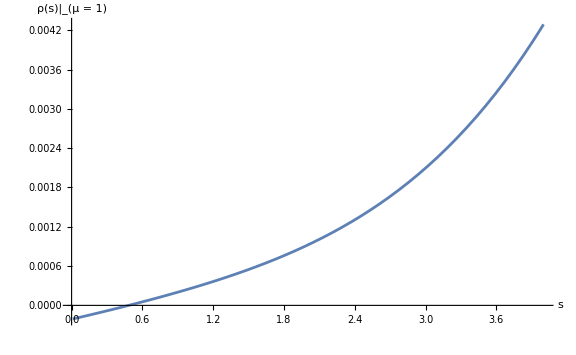
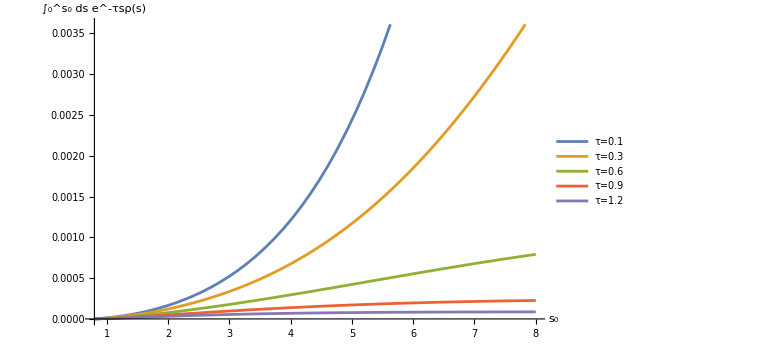

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

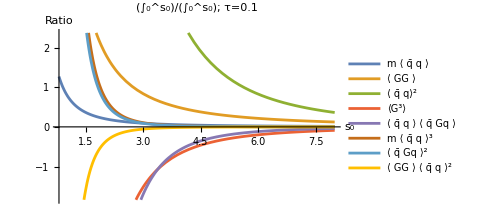
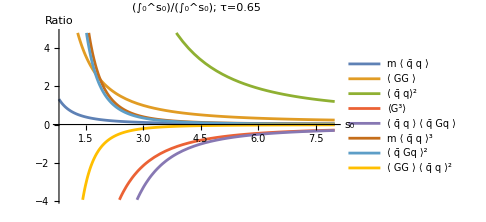
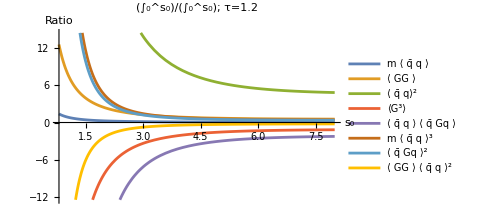

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

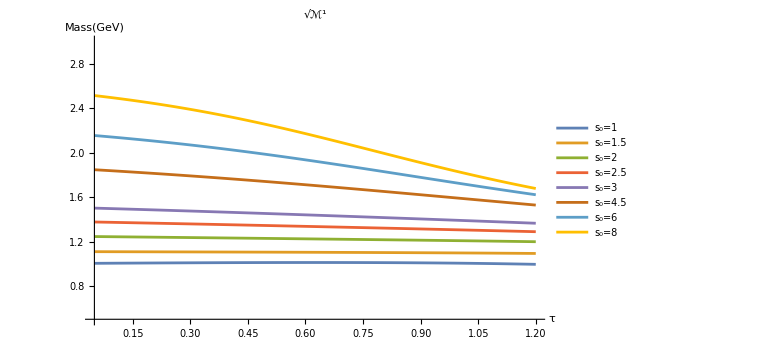
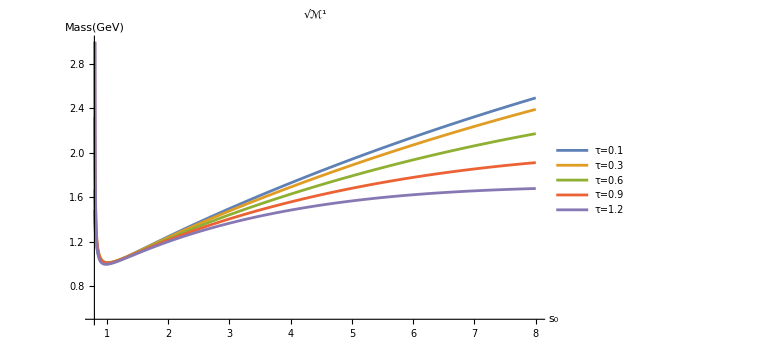

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

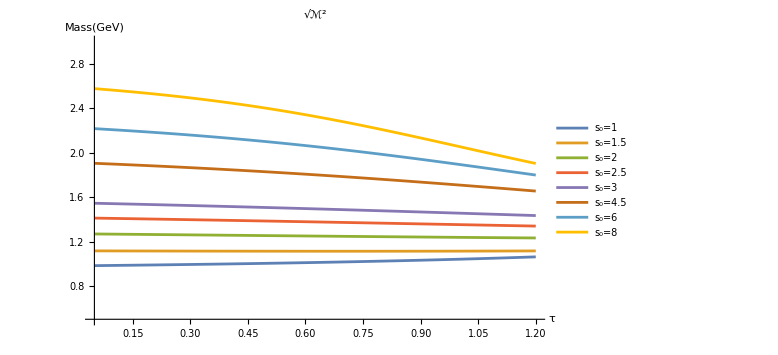
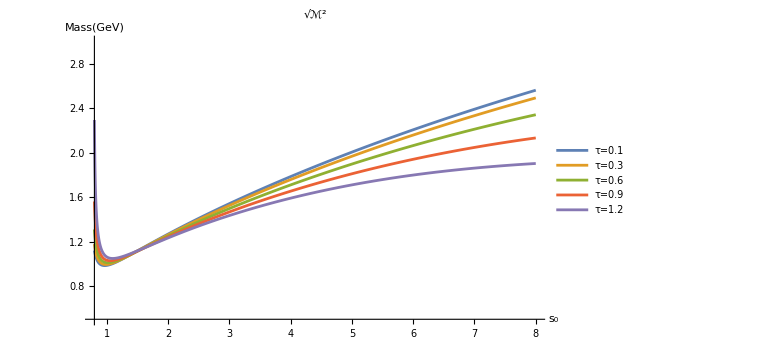

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

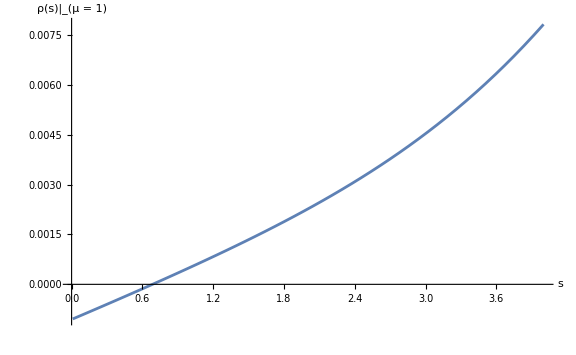
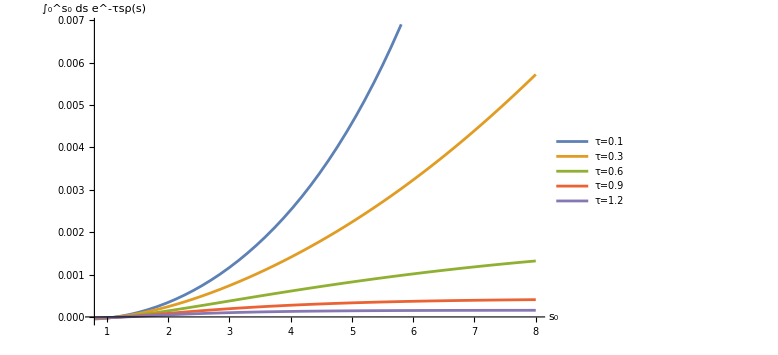

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

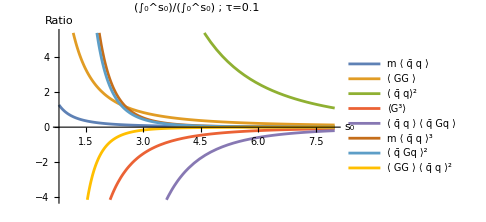
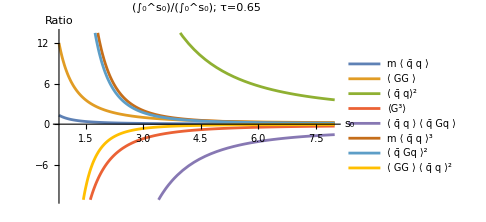
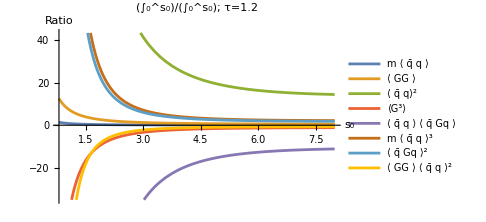

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

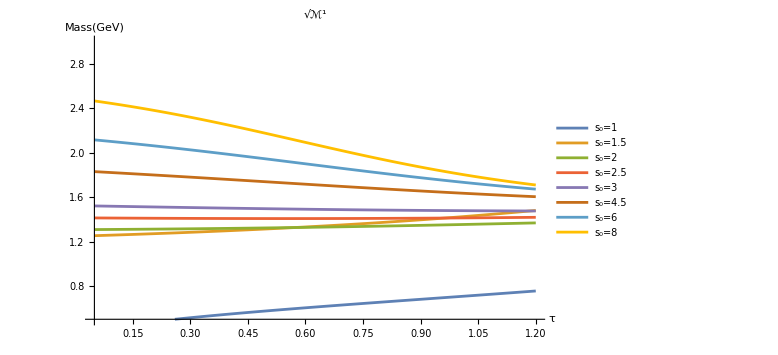
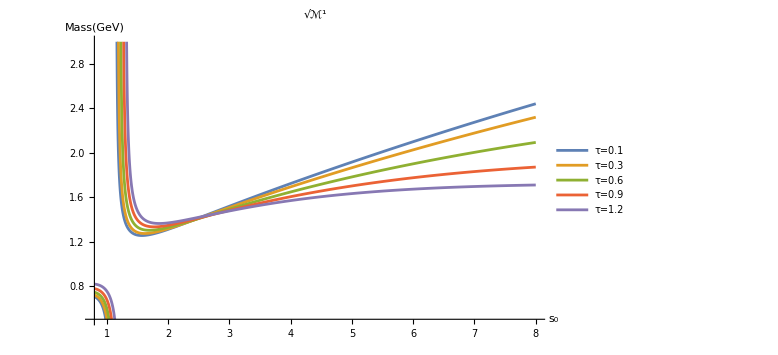

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5